```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/14/2010     

Assignment #2
Problem 2_b                                                    *)
```

```mathematica
Clear[a,b,fbas,f,fs,L,coeffs,fourier];
(*using a generic L until I can figure out how to introduce it as a variable*)
(*trying to figure out how to define functions as peicewise in mathematica*)
(*f[x_]:=x*(1+Abs[x])/;-1≤x<1;
f[x_]:=f[x+2]/;x≥1OR x<-1; 
f[1],f[3]  *)
```

```mathematica
L=1;
fbas[x_]:=(1-x)(1+x)^2/;-L≤x<L
f[x_]:=fbas[Mod[x,2×L,-L]]
```

```mathematica
N[f[3]]
```

0.

```mathematica
(*Defining the function as peicewise*)
```

```mathematica
(*g[x_]:=Piecewise[{{x*(1+Abs[x]),-1<=0<1},{f[x+2],x≥1}}];
g[3] *)
```

```mathematica
(*Defining the shifted function via Prof. Clark*)
```

```mathematica
(*defining the function to be approximated by the Fourier series*)
a[0]=N[Integrate[f[x],{x,-L,L}]]
```

1.33333

```mathematica
a[n_]=FullSimplify[(∫_-L^L (1-x)(1+x)^2*Cos[(n*Pi*x)/L]ⅆx)/(2L)]
```

(2 (-n π Cos[n π]+Sin[n π]))/(n^3 π^3)

```mathematica
b[n_]=FullSimplify[(∫_-L^L (1-x)(1+x)^2*Sin[(n*Pi*x)/L]ⅆx)/L]
```

-(4 (3 n π Cos[n π]+(-3+n^2 π^2) Sin[n π]))/(n^4 π^4)

```mathematica
coeffs=Table[{a[i],b[i]},{i,1,20}];
TableForm[coeffs]
```

2/π^2 | 12/π^3
-1/(2 π^2) | -3/(2 π^3)
2/(9 π^2) | 4/(9 π^3)
-1/(8 π^2) | -3/(16 π^3)
2/(25 π^2) | 12/(125 π^3)
-1/(18 π^2) | -1/(18 π^3)
2/(49 π^2) | 12/(343 π^3)
-1/(32 π^2) | -3/(128 π^3)
2/(81 π^2) | 4/(243 π^3)
-1/(50 π^2) | -3/(250 π^3)
2/(121 π^2) | 12/(1331 π^3)
-1/(72 π^2) | -1/(144 π^3)
2/(169 π^2) | 12/(2197 π^3)
-1/(98 π^2) | -3/(686 π^3)
2/(225 π^2) | 4/(1125 π^3)
-1/(128 π^2) | -3/(1024 π^3)
2/(289 π^2) | 12/(4913 π^3)
-1/(162 π^2) | -1/(486 π^3)
2/(361 π^2) | 12/(6859 π^3)
-1/(200 π^2) | -3/(2000 π^3)

```mathematica
coeffs[[1]]
```

{2/π^2,12/π^3}

```mathematica
coeffs[[2,1]]
```

-1/(2 π^2)

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

1.33333+(2 Cos[π x])/π^2-Cos[2 π x]/(2 π^2)+(2 Cos[3 π x])/(9 π^2)-Cos[4 π x]/(8 π^2)+(2 Cos[5 π x])/(25 π^2)+(12 Sin[π x])/π^3-(3 Sin[2 π x])/(2 π^3)+(4 Sin[3 π x])/(9 π^3)-(3 Sin[4 π x])/(16 π^3)+(12 Sin[5 π x])/(125 π^3)

```mathematica
fourier[10,x]
```

1.33333+(2 Cos[π x])/π^2-Cos[2 π x]/(2 π^2)+(2 Cos[3 π x])/(9 π^2)-Cos[4 π x]/(8 π^2)+(2 Cos[5 π x])/(25 π^2)-Cos[6 π x]/(18 π^2)+(2 Cos[7 π x])/(49 π^2)-Cos[8 π x]/(32 π^2)+(2 Cos[9 π x])/(81 π^2)-Cos[10 π x]/(50 π^2)+(12 Sin[π x])/π^3-(3 Sin[2 π x])/(2 π^3)+(4 Sin[3 π x])/(9 π^3)-(3 Sin[4 π x])/(16 π^3)+(12 Sin[5 π x])/(125 π^3)-Sin[6 π x]/(18 π^3)+(12 Sin[7 π x])/(343 π^3)-(3 Sin[8 π x])/(128 π^3)+(4 Sin[9 π x])/(243 π^3)-(3 Sin[10 π x])/(250 π^3)

```mathematica
Off[General::stop];
fourier[20,x]
```

1.33333+(2 Cos[π x])/π^2-Cos[2 π x]/(2 π^2)+(2 Cos[3 π x])/(9 π^2)-Cos[4 π x]/(8 π^2)+(2 Cos[5 π x])/(25 π^2)-Cos[6 π x]/(18 π^2)+(2 Cos[7 π x])/(49 π^2)-Cos[8 π x]/(32 π^2)+(2 Cos[9 π x])/(81 π^2)-Cos[10 π x]/(50 π^2)+(2 Cos[11 π x])/(121 π^2)-Cos[12 π x]/(72 π^2)+(2 Cos[13 π x])/(169 π^2)-Cos[14 π x]/(98 π^2)+(2 Cos[15 π x])/(225 π^2)-Cos[16 π x]/(128 π^2)+(2 Cos[17 π x])/(289 π^2)-Cos[18 π x]/(162 π^2)+(2 Cos[19 π x])/(361 π^2)-Cos[20 π x]/(200 π^2)+(12 Sin[π x])/π^3-(3 Sin[2 π x])/(2 π^3)+(4 Sin[3 π x])/(9 π^3)-(3 Sin[4 π x])/(16 π^3)+(12 Sin[5 π x])/(125 π^3)-Sin[6 π x]/(18 π^3)+(12 Sin[7 π x])/(343 π^3)-(3 Sin[8 π x])/(128 π^3)+(4 Sin[9 π x])/(243 π^3)-(3 Sin[10 π x])/(250 π^3)+(12 Sin[11 π x])/(1331 π^3)-Sin[12 π x]/(144 π^3)+(12 Sin[13 π x])/(2197 π^3)-(3 Sin[14 π x])/(686 π^3)+(4 Sin[15 π x])/(1125 π^3)-(3 Sin[16 π x])/(1024 π^3)+(12 Sin[17 π x])/(4913 π^3)-Sin[18 π x]/(486 π^3)+(12 Sin[19 π x])/(6859 π^3)-(3 Sin[20 π x])/(2000 π^3)

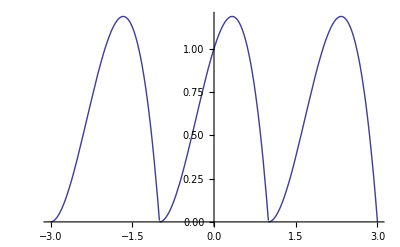

```mathematica
graphone=Plot[f[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

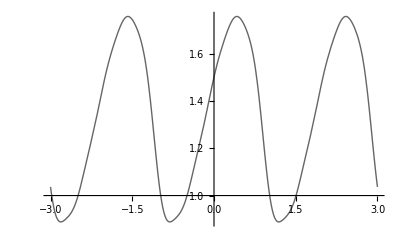

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

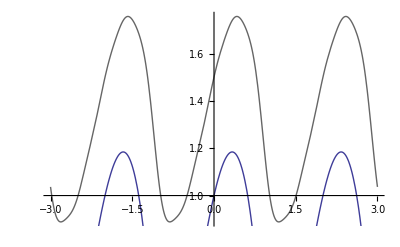

```mathematica
bothtwo=Show[graphtwo,graphone]
```

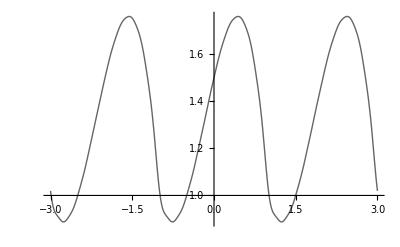

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

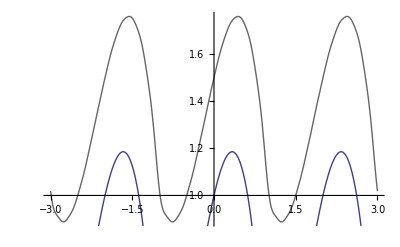

```mathematica
boththree=Show[graphthree,graphone]
```

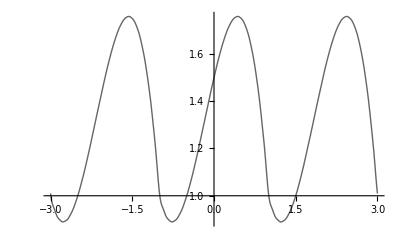

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

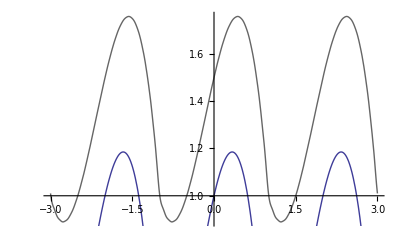

```mathematica
bothsix=Show[graphsix,graphone]
```

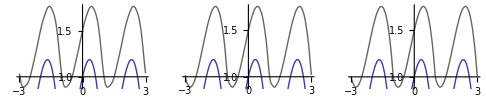

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```

```mathematica
(*  The rate of convergence of the series depends on the values of the fourier coefficients.  The values of the sine function oscillate between positive and negative one.  Therefore, the dependance of the fourier coefficients will determine how many terms will need to be computed and summed before the seires converges to a reasonable and arbitrary convergence on f(x), the function that it approximates.  As the net power of n in the denominator increases, it will take less and less terms for the series to converge.  A 1/n dependence i the fourier coefficient will take approx. 100 terms to reach 1% error, 1/n^2 will take approxamately 10, etc.  Also, the rate of convergence will decrease for functions with discontinuities (resulting in lower powers of n in the denominator).


*)
```